```mathematica
(* Volume of a solid enclosed by the paraboloid z=3x^2+4y^2 and the planes x = 0, y = 2, y = x, z = 2 *)
expr=3 x^2+4 y^2
```

3 x^2+4 y^2

```mathematica
Plot3D[expr, {x, -2, 2}, {y, -2,2}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
(* With planes: *)
ParametricPlot3D[{{0,u,v}, {u,2,v}, {u,u,v}, {u, v, 2}, {u, v,expr/.{x-> u, y-> v}}},{u, 0, 2}, {v,0,2}, AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
(* So, it's between π/4 ≤ θ ≤ π/2 *)
```

```mathematica
(* Let's do it in cylindrical coords *)
c=TransformedField["Cartesian"-> "Cylindrical",z==expr,{x,y,z}-> {r,θ,ζ}]//FullSimplify
```

ζ==-1/2 r^2 (-7+Cos[2 θ])

```mathematica
cs=Solve[c,r]//Flatten
```

{r→-(√2 √ζ)/(√(7-Cos[2 θ])),r→(√2 √ζ)/(√(7-Cos[2 θ]))}

```mathematica
Needs["VectorAnalysis`"]
𝒥=JacobianDeterminant[Cylindrical]/.Rr-> r
```

r

```mathematica
(* Full volume: *)
𝒱=∫_0^2 ∫_0^(2π) ∫_0^(r/. cs[[2]]) 1𝒥ⅆrⅆθⅆζ
```

π/(√3)

```mathematica
N[𝒱]
```

1.8138

```mathematica
(* Section volume: *)
s𝒱=∫_0^2 ∫_(π/4)^(π/2) ∫_0^(r/. cs[[2]]) 1𝒥ⅆrⅆθⅆζ
```

(π-2 ArcTan[2/(√3)])/(4 √3)

```mathematica
N[s𝒱]
```

0.206034

```mathematica
(* Approximately 1/8 of the total volume: *)
{s𝒱/𝒱,1/8}//N
```

{0.113593,0.125}

```mathematica
(* Find the equivalent circular paraboloid: *)
```

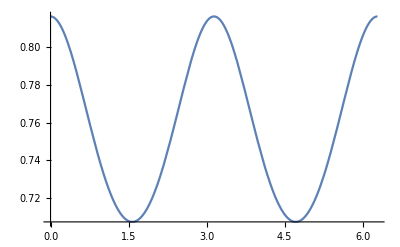

```mathematica
Plot[r//.{cs[[2]], ζ-> 2}, {θ,0,2π}]
```

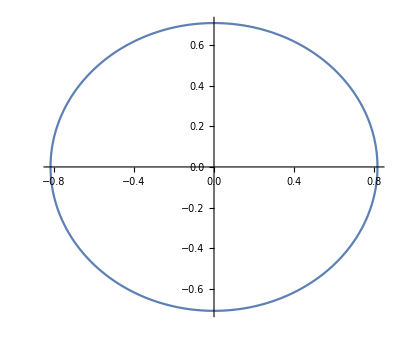

```mathematica
PolarPlot[r//.{cs[[2]], ζ-> 2}, {θ,0,2π}, AspectRatio-> Full]
```

```mathematica
r/.cs[[2]]
```

(√2 √ζ)/(√(7-Cos[2 θ]))

```mathematica
(* Semi-major axis: *)
Maximize[{(r/.cs[[2]]),0≤ θ≤ π, ζ>0}, θ,Reals]
```

Maximize[{(√2 √ζ)/(√(7-Cos[2 θ])),0≤θ≤π,ζ>0},θ,ℝ]

```mathematica
(* Manually: *)
Maximize[Cos[2θ],θ]
```

{1,{θ→0}}

```mathematica
a=(√2 √ζ)/(√(7-Cos[2 θ]))/.Cos[2θ]-> 1
```

(√ζ)/(√3)

```mathematica
(*Semi-minor axis: *)
Minimize[Cos[2θ],θ]
```

{-1,{θ→-(49 π)/2}}

```mathematica
b=(√2 √ζ)/(√(7-Cos[2 θ]))/.Cos[2θ]-> -1
```

(√ζ)/2

```mathematica
(* Radius of the circle of equivalent area: *)
r𝒞=√(a b)
```

(√ζ)/(√2 3^(1/4))

```mathematica
(* Volume of the circular paraboloid: *)
𝒱𝒞=∫_0^2 ∫_0^(2π) ∫_0^r𝒞 1𝒥ⅆrⅆθⅆζ
```

π/(√3)

```mathematica
𝒱==𝒱𝒞
```

True

```mathematica
(* Volume of the Cylinder of the same radius (and height 2): *)
r𝒞yl=r𝒞/.ζ-> 2
```

1/3^(1/4)

```mathematica
𝒱𝒞yl=∫_0^2 ∫_0^(2π) ∫_0^r𝒞yl 1𝒥ⅆrⅆθⅆζ
```

(2 π)/(√3)

```mathematica
𝒱𝒞/𝒱𝒞yl
```

1/2

```mathematica
(* Right *)
```